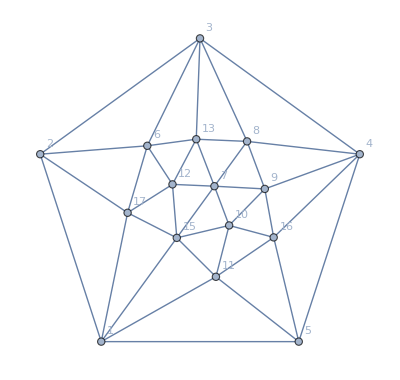

```mathematica
gr=VertexDelete[Graph[plantri8],14]
```

```mathematica
ChromaticPolynomial[gr,4]/24
```

63

```mathematica
forms=Select[FindFullFormula4[gr],HasQuadrilateralPattern[SymbolToSets[#]]&]
```

{v168ax24bcx37ghx59df,v168ax259dfx37ghx4bc,v14acx29bdx37ghx568f,v168gx24acx37bhx59df,v168gx259dfx37bhx4ac,v14adx29bcx37ghx568f,v137gx29bcx4adhx568f,v18acx24bdx37ghx569f,v14adx28bcx37ghx569f,v18cgx24adx37bhx569f,v14adx28cgx37bhx569f,v137gx28bcx4adhx569f,v137gx28acx4bdhx569f,v167gx258acx39fx4bdh,v167gx28bcx359fx4adh,v167gx28acx359fx4bdh,v18acx2dfgx359hx467b,v18cgx259dfx3ahx467b,v18cgx29dfx35ahx467b,v18acx259dfx3ghx467b,v167gx24dfx39bhx58ac,v1467x2dfgx39bhx58ac,v167gx258acx39bhx4df,v18acx259dfx37ghx46b,v146ax28bcx37ghx59df,v146ax28cgx37bhx59df,v18cgx259dfx37bhx46a,v13acx28fgx467bx59dh,v139cx28fgx467bx5adh,v1467x28fgx39bcx5adh,v167gx258fx39bcx4adh,v13cgx29dfx467bx58ah,v139cx2dfgx467bx58ah,v167gx24dfx39bcx58ah,v1467x2dfgx39bcx58ah,v168ax2dfgx359cx47bh,v168gx259dfx3acx47bh,v13cgx29dfx47bhx568a,v168gx29dfx35acx47bh,v168ax259dfx3cgx47bh,v139cx2dfgx47bhx568a}

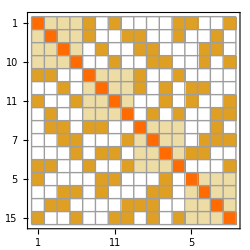
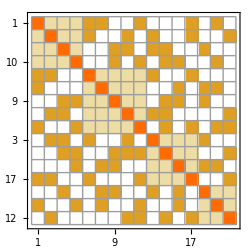
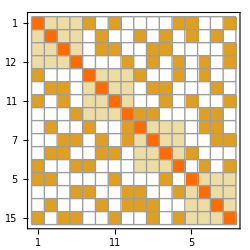
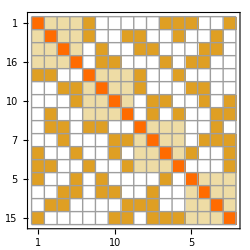
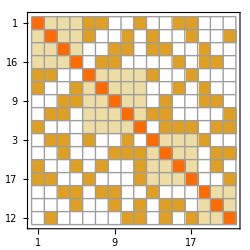
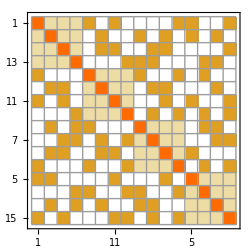
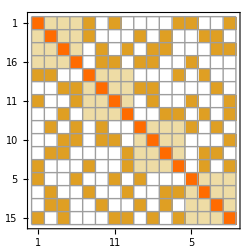
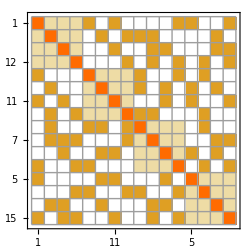
{-Graphics-v168ax24bcx37ghx59df,-Graphics-v168ax259dfx37ghx4bc,-Graphics-v14acx29bdx37ghx568f,-Graphics-v168gx24acx37bhx59df,-Graphics-v168gx259dfx37bhx4ac,-Graphics-v14adx29bcx37ghx568f,-Graphics-v137gx29bcx4adhx568f,-Graphics-v18acx24bdx37ghx569f,-Graphics-v14adx28bcx37ghx569f,-Graphics-v18cgx24adx37bhx569f,-Graphics-v14adx28cgx37bhx569f,-Graphics-v137gx28bcx4adhx569f,-Graphics-v137gx28acx4bdhx569f,-Graphics-v167gx258acx39fx4bdh,-Graphics-v167gx28bcx359fx4adh,-Graphics-v167gx28acx359fx4bdh,-Graphics-v18acx2dfgx359hx467b,-Graphics-v18cgx259dfx3ahx467b,-Graphics-v18cgx29dfx35ahx467b,-Graphics-v18acx259dfx3ghx467b,-Graphics-v167gx24dfx39bhx58ac,-Graphics-v1467x2dfgx39bhx58ac,-Graphics-v167gx258acx39bhx4df,-Graphics-v18acx259dfx37ghx46b,-Graphics-v146ax28bcx37ghx59df,-Graphics-v146ax28cgx37bhx59df,-Graphics-v18cgx259dfx37bhx46a,-Graphics-v13acx28fgx467bx59dh,-Graphics-v139cx28fgx467bx5adh,-Graphics-v1467x28fgx39bcx5adh,-Graphics-v167gx258fx39bcx4adh,-Graphics-v13cgx29dfx467bx58ah,-Graphics-v139cx2dfgx467bx58ah,-Graphics-v167gx24dfx39bcx58ah,-Graphics-v1467x2dfgx39bcx58ah,-Graphics-v168ax2dfgx359cx47bh,-Graphics-v168gx259dfx3acx47bh,-Graphics-v13cgx29dfx47bhx568a,-Graphics-v168gx29dfx35acx47bh,-Graphics-v168ax259dfx3cgx47bh,-Graphics-v139cx2dfgx47bhx568a}

```mathematica
Map[Labeled[DrawSolutionMatrix[gr,#],#]&,forms]
```

```mathematica
With[{all=Flatten[SymbolToSets[v137gx24bdx569fx8aehxc]]},Table[{i,all[[i]]},{i,Length[all]}]]//TableForm
```

1 | 1
2 | 3
3 | 7
4 | 16
5 | 2
6 | 4
7 | 11
8 | 13
9 | 5
10 | 6
11 | 9
12 | 15
13 | 8
14 | 10
15 | 14
16 | 17
17 | 12

```mathematica
mat=ContractMat[ContractMat[SolutionMatrix[plantri8,v137gx24bdx569fx8aehxc],3,16 ],2,7 ]
```

{{2,1,1,0,1,0,1,0,1,0,0,1,0,0,1,1,0},{1,2,0,1,1,1,2,1,1,1,0,1,1,1,1,0,0},{1,0,2,0,1,0,0,1,0,1,1,1,1,1,0,2,1},{0,1,0,2,0,1,1,0,1,0,1,0,0,1,0,0,0},{1,1,1,0,2,0,1,0,0,1,0,0,0,0,1,1,0},{0,1,0,1,0,2,1,0,1,0,1,0,1,0,1,0,0},{1,2,0,1,1,1,2,1,1,1,0,1,1,1,1,0,0},{0,1,1,0,0,0,1,2,0,1,0,0,1,0,0,1,1},{1,1,0,1,0,1,1,0,2,0,0,0,0,0,1,0,0},{0,1,1,0,1,0,1,1,0,2,0,0,0,0,0,1,1},{0,0,1,1,0,1,0,0,0,0,2,0,1,1,0,1,0},{1,1,1,0,0,0,1,0,0,0,0,2,0,1,0,1,1},{0,1,1,0,0,1,1,1,0,0,1,0,2,0,0,1,0},{0,1,1,1,0,0,1,0,0,0,1,1,0,2,0,1,0},{1,1,0,0,1,1,1,0,1,0,0,0,0,0,2,0,0},{1,0,2,0,1,0,0,1,0,1,1,1,1,1,0,2,1},{0,0,1,0,0,0,0,1,0,1,0,1,0,0,0,1,2}}

```mathematica
DrawMat[mat2_,sym_]:=Block[{ mat=mat2,colors=SymbolToColoring[sym], labels, size, ordered, start,newBucket},
size=Length[mat];
ordered=Flatten[SymbolToSets[sym]];
labels=Table[{k,Block[{res=Style[ordered[[k]],Darker[(ordered[[k]]/.colors)]]},
res]},{k,size}];
start=1;
Table[
newBucket=Table[k,{k,start,start+Length[bucket]-1}];
start+=Length[bucket];
Table[
Table[
mat[[row2,col2]]+=.1
,{col2,newBucket}
]
,{row2,newBucket}
]
,{bucket,SymbolToSets[sym]}
];
Column[
{
(*Graph[g,ImageSize->500,VertexStyle->colors]
,*)
MatrixPlot[ mat,Mesh->All, ImageSize->250,FrameTicks->{labels,labels,labels,labels}]
}
]
]
```

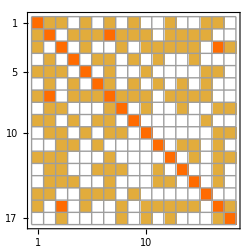

```mathematica
MatrixPlot[ mat,Mesh->All, ImageSize->250]
```

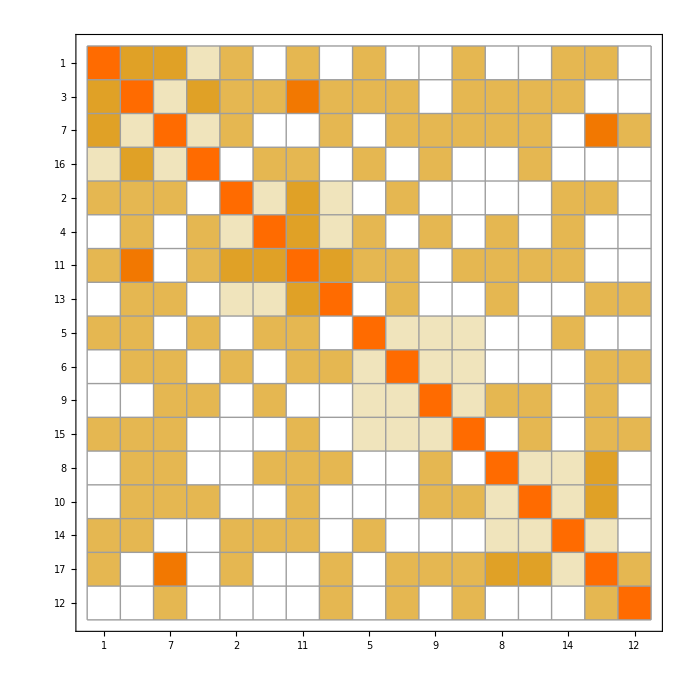

```mathematica
DrawMat[mat,v137gx24bdx569fx8aehxc]
```

```mathematica
allGraphs5[gamma1Key,"graph"]
```

-Graphics-

```mathematica
Block[{g,forms},
g=plantri8;
forms=FindFullFormula5[g]
]
```

{v137gx24bdx569fx8aehxc,v137gx24bdx58ahx69efxc,v167gx24bdx359fx8aehxc,v168ax24bdx359fx7eghxc,v14adx257x39bhx68efgxc,v147x25adx39bhx68efgxc,v1adx247bx359hx68efgxc,v14adx27bx359hx68efgxc,v137gx24adx568fx9behxc,v137gx24adx569fx8behxc,v14adx28fgx359hx67bexc,v1467x25adx39bhx8efgxc,v14adx258fx39bhx67egxc,v167gx24adx359fx8behxc,v14adx259fx37ghx68bexc,v14adx259fx37bhx68egxc,36250,v14ax2dfgx39bcx57hx68e,v14ax2dfgx39bcx568x7eh,v13acx24dfx57hx68gx9be,v13acx24dfx568x7ghx9be,v168ax24dfx35cx7ghx9be,v168ax24dfx3cgx57hx9be,v168ax24dfx39bcx5x7egh,v13acx24dfx568x7eghx9b,v1ax24dfx39bcx568x7egh,v13acx24dfx57hx68egx9b,v168ax24x39bcx57hxdefg,v1ax24dfx39bcx57hx68eg,v168ax24dfx39bcx57hxeg,v168ax24x39bcx5dfx7egh,v168ax24dfx35cx7eghx9b}
 |  |  |  |